Notebook Setup

```mathematica
Remove["Global`*"](*Clears all variables*)

SetOptions[EvaluationNotebook[],AutoStyleOptions->{"CommentStyle"->{FontColor->Blue,FontFamily->"Helvetica",FontSize->10,FontWeight->"Thin"}}]; (*Comments are set to be blue and thin*)

SetOptions[Plot,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True]; (*Sets Plots to have a certain color scheme and to use a frame*)

SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->18},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True,FrameTicks->{Automatic,Automatic},ImagePadding->{{70, 10}, {50, 10}}]; (*Sets ListPlots to have a certain color scheme and to use a frame*)
```

Physics Setup

```mathematica
μs=10^-6; (*Units*)
MHz=10^6;
GHz=10^9;
PS=2π 222 MHz; (*Stokes Rabi frequency*)
PP=2π 37 MHz; (*Pump Rabi frequency*)
Γ=2π 100 MHz; (*Scattering from intermediate states*)
tmax=20; (*Length of time, in μs, that the simulation runs for. Typically τ+w. *)
precision=10; (*Significant figures used for numerical simulations like NDSolve.*)
H[t_,τ_,w_]=({{0, 1/2 Ωp[t,τ,w], 1/2 Ωpp[t,τ,w], 0}, {1/2 Ωp[t,τ,w], Δp[t,τ,w]-ⅈ Γ/2, 0, 1/2 Ωs[t,τ,w]}, {1/2 Ωpp[t,τ,w], 0, Δp[t,τ,w]+2π(133.86-130.41)GHz-ⅈ Γ/2, 0}, {0, 1/2 Ωs[t,τ,w], 0, Δp[t,τ,w]-Δs[t,τ,w]}}); (*Hamiltonian for the 4-level Λ system, where the levels are the initial, intermediate, detuned intermediate, and final states respectively. We can ignore the detuned state by turning off Ωpp. *)

H3STIRAP[t_,τ_,w_]=H[t,τ,w]/.{Ωs[t,τ,w]->Piecewise[{{PS/(√1.3-√(.3))(√1.3-√(((t-w/2)/(w/2))^2+0.3)), 0<t<w}}] ,Ωp[t,τ,w]->Piecewise[{{PP/(√1.3-√(.3))(√1.3-√(((t-τ-w/2)/(w/2))^2+0.3)), τ<t<τ+w}}],Δp[t,τ,w]->0,Δs[t,τ,w]->0,Ωpp[t,τ,w]->0}; (*Hamiltonian for the 3-level system, without detuning*)

H4STIRAP[t_,τ_,w_]=H[t,τ,w]/.{Ωs[t,τ,w]->Piecewise[{{PS/(√1.3-√(.3))(√1.3-√(((t-w/2)/(w/2))^2+0.3)), 0<t<w}}] ,Ωp[t,τ,w]->Piecewise[{{PP/(√1.3-√(.3))(√1.3-√(((t-τ-w/2)/(w/2))^2+0.3)), τ<t<τ+w}}],Δp[t,τ,w]->0,Δs[t,τ,w]->0,Ωpp[t,τ,w]->Piecewise[{{(12 PP)/(√1.3-√(.3))(√1.3-√(((t-τ-w/2)/(w/2))^2+0.3)), τ<t<τ+w}}]}; (*Hamiltonian for thH4e 4-level system, without detuning*)
H3DRAMAN[t_,τ_,w_]=H[t,τ,w]/.{Ωs[t,τ,w]->Piecewise[{{PS, 0<t<w}}] ,Ωp[t,τ,w]->Piecewise[{{PP, τ<t<τ+w}}],Δp[t,τ,w]->Piecewise[{{2π 20GHz, τ<t<τ+w}}],Δs[t,τ,w]->Piecewise[{{2π 20 GHz, 0<t<w}}],Ωpp[t,τ,w]->0}; (*Hamiltonian for the 3-level system, without detuning*)
```

Eigen-energies and Eigenstates

```mathematica
adComp[t0_,τ0_,w0_,H0_]:=Module[{t=t0,τ=τ0,w=w0,Ham=H0},
{evals,evecs}=Eigensystem[Ham[t μs,τ μs,w μs]];(*obtain the eigenvalues and eigenvectors of the Hamiltonian for given t, τ and w parameters*)
evals=Re[evals]; (*We are only interested in the state energies, which are the real component of the eigenvalues*)
evecs=Chop[Table[evecs⟦i⟧/(evecs⟦i⟧.evecs⟦i⟧*),{i,1,4}],10^-7]; (*Normalize the eigenvectors. Note that the eigenvectors are complex due to the scattering term. Chop removes small terms that arise from numerical errror.*)
order=Ordering[Table[Abs[evecs⟦i⟧.Normalize[{0,1,2,0}]],{i,1,4}]]; (*We order the eigenvectors by how much they contain the intermediate states, such that the first in the order should correspond to the adiabatic state. We dot against {0,1,2,0} because the adiabatic state is always ordered first. This is as opposed to {0,1,1,0}, where sometimes a different state has a smaller dot product. That typically occurs when there is an energy crossing.*)
advec=evecs⟦order⟧⟦1⟧;(*When the eigenvectors are ordered, the first should correspond to the adiabatic state, which we call advec*)
advec=Table[advec⟦i⟧*advec⟦i⟧*,{i,1,4}]//Re;(*advec can be imaginary, but we are interested in the magnitude in each component. So we multiply each component by its complex conjugate. The //Re tells Mathematica that the elements of advec are real, as they should be. *)
adval=evals⟦order⟧⟦1⟧;(*We find the eigenenergy of the adiabatic state. The same order is appropriate, since Eigensystem pairs eigenvalues with eigenvectors automatically.*)
{Sort[evals],adval,advec}](*These are the three outputs used for visualizing the state evolution in various plots: the eigenenergies, the adiabatic energy, and the adiabatic state*)
```

Schrodinger Equation

```mathematica
pops[H0_]:=Module[{Ham=H0},
P[t_]={p1[t],p2[t],p3[t],p4[t]};(*We define the population in each of the four bare basis states to be time dependent*)
init=P[0]=={1,0,0,0};(*We set the population to initially reside in the initial state*) 
SE=ⅈ P'[t]==Ham[t,τ,w ].P[t];(*The Schrodinger equation*)
PSoln=ParametricNDSolve[{SE,init},{p1,p2,p3,p4},{t,0,20 μs},{τ,w},PrecisionGoal->precision];(*We solve the Schrodinger equation parametrically, such that we obtain numerical solutions for the four populations as a function of τ and w.*)
PSoln (*The module outputs the four time-dependent populations, which are functions of τ and w.*)]
```

Visualize

```mathematica
padding={{70, 10}, {50, 10}}; (*padding, aspect ratio, and size set each plot to occupy the same space on screen. *)
aratio=0.5;
size=500;
step=0.01; (*The time, in μs, used between points in the ListPlot.*)
seePulses[τ_,w_,Ham_]:=Plot[Evaluate[{1/(2π MHz)2Ham[t μs,τ μs,w μs]⟦2,4⟧,1/(2π MHz)2Ham[t μs,τ μs,w μs]⟦1,2⟧,1/(2π MHz)(Re[Ham[t μs,τ μs,w μs]⟦2,2⟧]-Ham[t μs,τ μs,w μs]⟦4,4⟧),1/(2π MHz)Re[Ham[t μs,τ μs,w μs]⟦2,2⟧]}],{t,0,τ+w},PlotRange->All,ImagePadding->padding,ImageSize->size,AspectRatio-> aratio,FrameLabel->{"Time (μs)","Frequency (MHz)"},PlotLegends->Placed[LineLegend[{"Ωs","Ωp","Δs","Δp"},LabelStyle->18],{0.8,.5}],PlotLabel->"Pulse"] (*plots Ωs, Ωp, Δs, and Δp*)

seeEvals[τ_,w_,Ham_]:=Plot[{1/(2π MHz)adComp[t,τ,w,Ham]⟦1⟧⟦1;;3⟧,1/(2π MHz)adComp[t,τ,w,Ham]⟦2⟧},{t,0,τ+w},PlotRange->All,ImagePadding->padding,ImageSize->size,AspectRatio-> aratio,FrameLabel->{"Time (μs)","Energy (MHz)"},PlotLabel->"Eigenvalues"](*plot of eigenenergies, excluding the highly detuned excited state. The adiabatic state is in blue.*)

seeAdFrac[τ_,w_,Ham_]:=ListPlot[Table[Table[{t,adComp[t,τ,w,Ham]⟦3⟧⟦i⟧},{t,0,τ+w-step,step}],{i,1,4}],ImagePadding->padding,ImageSize->size,AspectRatio-> aratio,FrameLabel->{"Time (μs)",""},PlotLegends->Placed[LineLegend[{"Initial","Int.","Int. Detuned","Final"},LabelStyle->18],{0.8,.5}],PlotLabel->"Adiabatic State Fraction"](*plot of the fraction of the adiabatic state in the original basis, over time*)

seePops[τ_,w_,Ham_]:=Plot[Evaluate@({Abs[p1[τ μs,w μs][t μs]]^2,100 Abs[p2[τ μs,w μs][t μs]]^2,100 Abs[p3[τ μs,w μs][t μs]]^2,Abs[p4[τ μs,w μs][t μs]]^2}/.pops[Ham]),{t,0,τ+w-step },PlotRange->All,PlotLegends->Placed[LineLegend[{"Initial","Int.","Detuned Int.","Final"},LabelStyle->18],{0.8,.5}],FrameLabel->{"Time (μs)","Population"},FrameTicks->Automatic,ImageSize->size,PlotLabel->"Population 4-state"](*plot of the population transfer over time in the original basis*)
```

Output

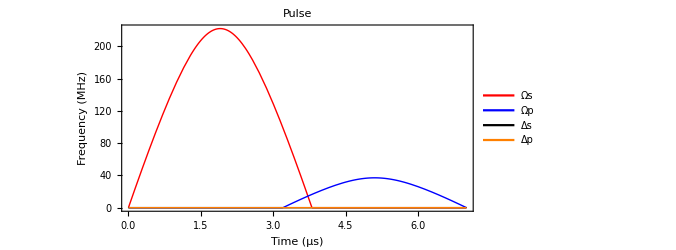
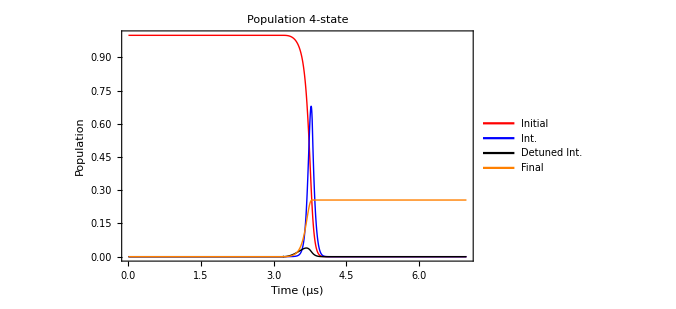
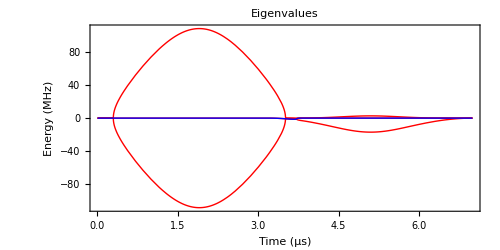
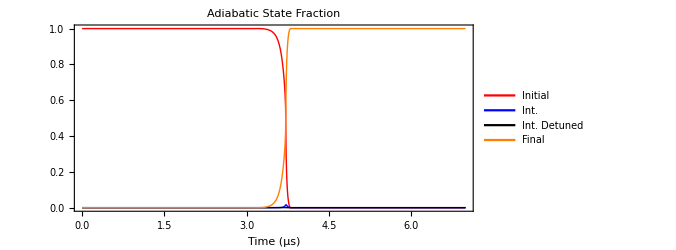

```mathematica
τTest=3.2;wTest=3.8;
{seePulses[τTest,wTest,H4STIRAP],seePops[τTest ,wTest ,H4STIRAP],seeEvals[τTest,wTest,H4STIRAP],seeAdFrac[τTest,wTest,H4STIRAP]}
(*seeAdFrac[1,10,H3STIRAP]*)
```

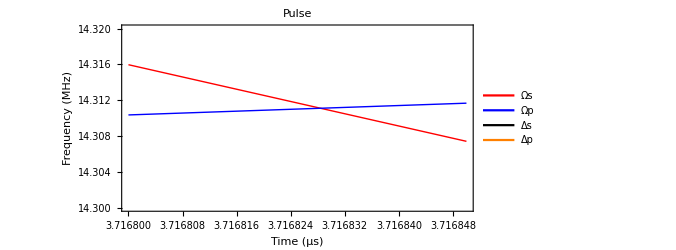

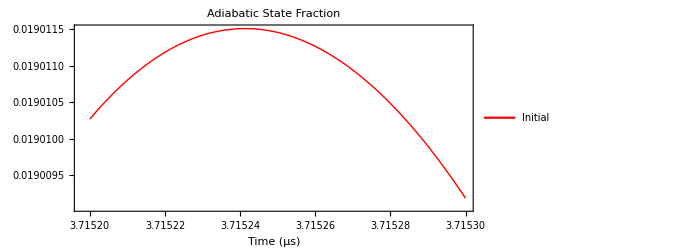

```mathematica
τTest=3.2;wTest=3.8;
Plot[Evaluate[{1/(2π MHz)2H4STIRAP[t μs,τTest μs,wTest μs]⟦2,4⟧,1/(2π MHz)2H4STIRAP[t μs,τTest μs,wTest μs]⟦1,2⟧,1/(2π MHz)(Re[H4STIRAP[t μs,τTest μs,wTest μs]⟦2,2⟧]-H4STIRAP[t μs,τTest μs,wTest μs]⟦4,4⟧),1/(2π MHz)Re[H4STIRAP[t μs,τTest μs,wTest μs]⟦2,2⟧]}],{t,3.7168,3.71685},PlotRange->{14.30,14.32},ImagePadding->padding,ImageSize->size,AspectRatio-> aratio,FrameLabel->{"Time (μs)","Frequency (MHz)"},PlotLegends->Placed[LineLegend[{"Ωs","Ωp","Δs","Δp"},LabelStyle->18],{0.8,.5}],PlotLabel->"Pulse"] (*plots Ωs, Ωp, Δs, and Δp*)
ListPlot[Table[Table[{t,adComp[t,τTest,wTest,H4STIRAP]⟦3⟧⟦i⟧},{t,3.7152,3.7153,.000001}],{i,2,2}],ImagePadding->padding,ImageSize->size,AspectRatio-> aratio,FrameLabel->{"Time (μs)",""},PlotLegends->Placed[LineLegend[{"Initial","Int.","Int. Detuned","Final"},LabelStyle->18],{0.8,.5}],PlotLabel->"Adiabatic State Fraction"]
```